# Elliptical Constraints Figures

I need 2D and 3D figures illustrating the construction

## 2D

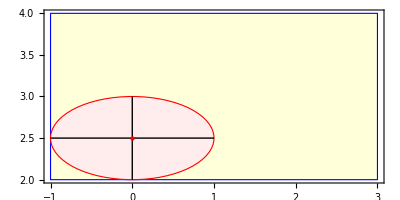

```mathematica
{l,u}={{-1,2},{3,4}};
vars={x,y};
c={0,2.5};
r=Map[Min,{c-l,u-c}ᵀ];
Graphics[{
{EdgeForm[Blue],LightYellow,Rectangle[l,u]},
{EdgeForm[Red],LightPink,Disk[c,r]},
Line[{c-{0,r⟦2⟧},c+{0,r⟦2⟧}}],
Line[{c-{r⟦1⟧,0},c+{r⟦1⟧,0}}],
{Red, Point[c]}
},
AspectRatio->Automatic,
Frame->True,
PlotRangePadding->0.2]
```

## 3D

```mathematica
{l,u}={{-1,2},{3,4}};
vars={x,y};
c={0,2.5};
r=Map[Min,{c-l,u-c}ᵀ];
BoxBounds=Apply[And,Table[ l⟦i⟧<vars⟦i⟧ <u⟦i⟧,{i,Length[vars]}]];
Show[
RegionPlot[ BoxBounds,{x,-2,4},{y,1,5},
PlotPoints->100,
PlotStyle->LightYellow],
Graphics[{
{EdgeForm[Red],LightPink,Disk[c,r]},
Line[{c-{0,r⟦2⟧},c+{0,r⟦2⟧}}],
Line[{c-{r⟦1⟧,0},c+{r⟦1⟧,0}}],
{Red, Point[c]}
}],
AspectRatio->Automatic
]
```

```mathematica
{l,u}={{-1,2,1},{3,4,6}};
vars={x,y,z};
c={0,2.5,1.2};
r=Map[Min,{c-l,u-c}ᵀ];
BoxBounds=Apply[And,Table[ l⟦i⟧<vars⟦i⟧ <u⟦i⟧,{i,Length[vars]}]];
Show[
RegionPlot3D[ BoxBounds,{x,-2,4},{y,1,5},{z,0, 7},
PlotPoints->100,
PlotStyle->Opacity[0.0]],
Graphics3D[{
{EdgeForm[Red],LightPink,Ellipsoid[c,r]},
Line[{c-{0,r⟦2⟧,0},c+{0,r⟦2⟧,0}}],
Line[{c-{r⟦1⟧,0,0},c+{r⟦1⟧,0,0}}],
{Red, Point[c]}
}]
]
```

-Graphics3D-

```mathematica
?Disk
```